```mathematica
(*Quiz 3*)
(*3.1*)
(*Write a function that converts speed in MPH to m/s*)
meterps[x_] := x*1609.3/3600
```

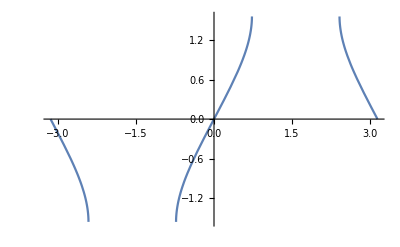

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{theta1→0.729728}}

{41.8103}

```mathematica
(*3.2*)
(*Compute &plot theta2*)
theta2[n1_, n2_, theta1_] := ArcSin[(n1*Sin[theta1])/n2]
Plot[theta2[1.5,1,theta1],{theta1,-Pi,Pi}]
(*Solve for critical angle for total internal reflection*)
Solve[theta2[1.5,1,theta1]==(Pi/2),theta1]
degrees = N[theta1(180/Pi)/.%]
```

```mathematica
(*3.3*)
taylorcoeffs[n_,exp_,var_]:=Table[var^i(D[exp,{var,i}]/.var->0)/i!,{i,0,n}]
taylorcoeffs[6,ⅇ^z,z]
taylorcoeffs[11,ArcTanh[w],w]
```

{1,z,z^2/2,z^3/6,z^4/24,z^5/120,z^6/720}

{0,w,0,w^3/3,0,w^5/5,0,w^7/7,0,w^9/9,0,w^11/11}

```mathematica
(*3.4*)
(*Solve the system of equations given*)
(*replaced x,y,z with a,b,c*)
eq1 = 2a-3b+4c==-1
eq2=-1a+2b+c==8
eq3=3a+b-2c==-3
Solve[{eq1,eq2,eq3},{a,b,c}]
```

2 a-3 b+4 c==-1

-a+2 b+c==8

3 a+b-2 c==-3

{{a→-22/41,b→111/41,c→84/41}}

{{2,xxx,5},{xxx,-1,0},{-1,6,xxx/2}}

{{xxx→-7.70056},{xxx→0.172502},{xxx→7.52806}}

{{xxx→-7.70056},{xxx→0.172502},{xxx→7.52806}}

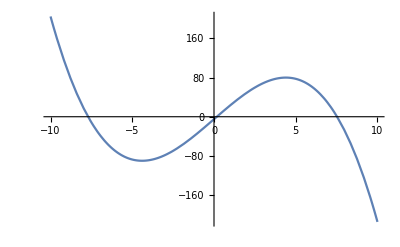

```mathematica
(*3.5*)
(*replaced x with xxx*)
matrix3={{2,xxx,5},{xxx,-1,0},{-1,6,xxx/2}}
N[Solve[Det[matrix3] ==0,xxx]]
Chop[%]
Plot[Det[matrix3],{xxx,-10,10}]
```